# <S_R> Of perturbed markov processes

## Set up and Functions - Run this first

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
font=35;
fontsize=22;
lineSize=17;
```

### Probability of choosing a “1” in the topology matrix is “q”

```mathematica
q=0.5;
Rand[q_]:=RandomChoice[{q,1-q}->{1,0}]
```

### Create a random markov matrix according to the distribution

```mathematica
Clear[d];
d[i_,j_,n_]:=Min[{Abs[i-j],n-Abs[i-j]}];
```

```mathematica
MakeCloseConnectedMatrix:=Function[{β,n},
Block[{d},
d[i_,j_]:=Min[{Abs[i-j],n-Abs[i-j]}];
Table[If[RandomReal[]<Exp[-β d[i,j]](*&&i≠j*),1,0],{i,1,n},{j,1,n}]
]
];
```

```mathematica
MakeCloseConnectedDiffusion:=Function[{β,n},
Block[{S,a,r},
S=MakeCloseConnectedMatrix[β,n];
a=S;
r=Table[Total[S⟦i⟧],{i,1,n}];
Table[a⟦i,j⟧/r⟦i⟧,{i,1,n},{j,1,n}]
]
];
```

```mathematica
MakeCloseConnectedMatrixNoDiag:=Function[{β,n},
Block[{d,A,sum,i},

A=Table[If[RandomReal[]<Exp[-β d[i,j]]&&i≠j,1,0],{i,1,n},{j,1,n}];
sum=Total[Transpose[A]];
For[i=1,i≤n,++i,If[sum⟦i⟧==0,A⟦i,i⟧=1]];
A
]
];
```

```mathematica
MakeCloseConnectedDiffusionNoDiag:=Function[{β,n},
Block[{S,a,r},
S=MakeCloseConnectedMatrixNoDiag[β,n];
a=S;
r=Table[Total[S⟦i⟧],{i,1,n}];
Table[a⟦i,j⟧/r⟦i⟧,{i,1,n},{j,1,n}]
]
];
```

```mathematica
MakeExponentialDiffusion:=Function[{β,n},
Block[{d,clamp,S,a,r,sum,i},
d[i_,j_]:=Min[{Abs[i-j],n-Abs[i-j]}];
clamp[x_]:=If[x>0,x,0];
S=Table[clamp[ⅇ^(-β d[i,j])RandomVariate[NormalDistribution[]]],{i,1,n},{j,1,n}];
sum=Total[Transpose[S]];
For[i=1,i≤n,++i,If[sum⟦i⟧==0,S⟦i,i⟧=1]];
S/(Total/@S)
]
];
```

### Create a Markov matrix out of any matrix with non-negative entries

```mathematica
Probabilize:=Function[{M},
Block[{n=Length[M],r},
r=Table[Sum[N[M⟦j,i⟧],{i,1,n}],{j,1,n}];
Table[If[r⟦j⟧>0,M⟦j,i⟧/r⟦j⟧,If[i==j,1,0]],{j,1,n},{i,1,n}]
]
]
```

### Create a Prior Probability

```mathematica
UniformP[k_]:=Table[1./k,{i,1,k}]
```

```mathematica
RandomP:=Function[{k},
Block[{lst},
lst=Sort[Prepend[Append[Table[RandomReal[],{k-1}],1],0]];
Table[lst⟦i+1⟧-lst⟦i⟧,{i,1,k}]
]
];
```

### Entropy function

```mathematica
H[pr_]:=-pr.Log[pr]
```

### Custom Matrix Power function

```mathematica
MP[M_,s_]:=If[s>0,MatrixPower[M,s],IdentityMatrix[Length[M]]];
```

### Custom log, log(0)=0

```mathematica
zLog[x_]:=If[x==0,0,Log[x]]
```

### Helper functions

```mathematica
Id[k_]:=If[k==0,0,1]
IdC[k_]:=1-Id[k];
Clamp[k_]:=If[k≠0,k,1];
(* First order matrix variation *)
DM:= Function[{A,s,α,β},
Block[{n=Length[A]},
Table[Sum[N[MP[A,k-1]⟦i,α⟧(MP[A,s-k]⟦β,j⟧-MP[A,s-k+1]⟦α,j⟧)],{k,1,s}],{i,1,n},{j,1,n}]
]
];
```

### Entropy related functions, given a transition matrix M

```mathematica
Clear[Np,ST,SP,SN,SR];
Np:=Function[{M,i,s,P},
P.MP[M,s];
];
ST:=Function[{M,s,P},
Block[{n=Length[M],mp=MP[M,s]},
-Sum[P⟦j⟧mp⟦j,i⟧zLog[mp⟦j,i⟧],{i,1,n},{j,1,n}]
]
];
SP:=Function[{P},
Block[{n=Length[P]},
-Sum[P⟦j⟧Log[P⟦j⟧],{j,1,n}]
]
]
SN:=Function[{M,s,P},
Block[{n=Length[M],mp,np},
mp=MP[M,s];
(* This is the same as using Np[M,i,s] *)
np=P.mp;
-Sum[np⟦i⟧zLog[np⟦i⟧],{i,1,n}]
]
];
SR:=Function[{M,s,P},
ST[M,s,P]+SP[P]-SN[M,s,P]
];
```

#### Perturbation operator

```mathematica
Δ:=Function[{M,α,β,ϵ},
(* Have to manually make sure we don't subtract too much from 0 elements *)
If [M⟦α,β⟧(1-ϵ)+ϵ<0,
(* No change *)
M,
(* Otherwise *)
Block[{τ,n=Length[M],R,j},
(* Temporary matrix *)
R=M;
(* Add the primary variation *)
R⟦α,β⟧+=ϵ;
(* Add correction *)
For[j=1,j≤n,++j,R⟦α,j⟧-=M⟦α,j⟧*ϵ];
R
]
]
];
```

#### Make a table of the ϵ perturbation in S_R for every element

```mathematica
MakeDSRTable:=Function[{A,s,ϵ,P},
(* Checks *)
If[Length[P]≠Length[A],Throw["Error"]];
(* Create table *)
Block[{SR0,n=Length[A]},
SR0=SR[A,s,P];
Table[SR[Δ[A,i,j,ϵ],s,P]-SR0,{i,1,n},{j,1,n}]
]
];
```

```mathematica
MakeDSTTable:=Function[{A,s,ϵ,P},
(* Checks *)
If[Length[P]≠Length[A],Throw["Error"]];
(* Create table *)
Block[{ST0,n=Length[A]},
ST0=ST[A,s,P];
Table[ST[Δ[A,i,j,ϵ],s,P]-ST0,{i,1,n},{j,1,n}]
]
];
```

#### Functions for creating images of weighted adjacency matrices

```mathematica
(* Function for creating a list that can be used with EdgeStyle->. Widths reflect connection strength *)
CreateWeightIndicators:=Function[{M,μ,cut,arrowsize},
Block[{i,j,n=Length[M]},
Reap[
For[i=1,i≤n,++i,
For[j=1,j≤n,++j,
If[M⟦i,j⟧>0&&M⟦i,j⟧≠∞,
If[M⟦i,j⟧<cut,
Sow[(i->j->{Dashed,Thin})],
Sow[(i->j->Directive[Thickness[μ M⟦i,j⟧],Arrowheads[arrowsize×M⟦i,j⟧]])]
]]]]]⟦2⟧⟦1⟧]]
```

```mathematica
(* Function that turns 0 -> ∞ for the creation of weighted adjacency matrices *)
MakeWeightedAdjacency:=Function[{A,cut,showWeights,thickness},
Table[If[A⟦i,j⟧≤0,∞,If[A⟦i,j⟧≤cut,∞,If[showWeights,A⟦i,j⟧,thickness]]],{i,1,Length[A]},{j,1,Length[A]}]
]
```

```mathematica
(* Function that displays a weighted adjacency graph from its adjacency matrix *)
Clear[CreateWeightedGraphImageFull,CreateWeightedGraphImage];
CreateWeightedGraphImageFull:=Function[{A,cut,arrowsize,showWeights,thickness,vertexsize},
Block[{wa,μ=0.015,style},
wa=MakeWeightedAdjacency[A,cut,showWeights,thickness];
If[showWeights,
style=CreateWeightIndicators[wa,μ,cut,arrowsize],
style=Directive[Thickness[0.5μ],Arrowheads[arrowsize]]
];
WeightedAdjacencyGraph[
wa,
DirectedEdges->True,GraphStyle->"BasicBlack",VertexStyle->Red,VertexSize->vertexsize,EdgeStyle->style
(*GraphLayout->"HighDimensionalEmbedding"*)
]
]
(* *)
]
(* vertexsize was 0.3 *)
CreateWeightedGraphImage[A_,showWeights_:False,cut_:0.025,arrowsize_:0.05,thickness_:0.4,vertexsize_:0.3]:=CreateWeightedGraphImageFull[A,cut,arrowsize,showWeights,thickness,vertexsize]
```

```mathematica
ZeroOne[x_]:=If[x>0,1,0]
```

```mathematica
MakeGraph[network_]:=AdjacencyGraph[Map[ZeroOne,network,{2}],EdgeStyle->{Thick,Black},VertexStyle->{Red},VertexSize->Medium]
```

#### Create a random matrix, ascend the S_R gradient to maximize, returns a list Format: { { {λ_0,S_R(0)}, ... , {λ_k,S_R(k)} }, {λ_0,S_T(0)}, ... , {λ_k,S_T(k)} }, { A(0), ... , A(k) } }

```mathematica
(* Non-introducing version - NI==True - only modifies preexisting edges *)
Clear[GeneralPerturbationGradientAscendBase,GeneralPerturbationGradientAscend];
GeneralPerturbationGradientAscendBase:=Function[{A,s,ϵ,steps,TableFunction,P,noise},
Block[{n=Length[A],S=A,sr,st,iter=0,oldS,table,str,vector,i,j,aϵ=Abs[ϵ],acc=0},
(* Gradient ascend for Matrix S *)
sr=SR[S,s,P];
st=ST[S,s,P];
Reap[
(* Sow initial data *)
Sow[{iter,sr},1];
Sow[{iter,st},2];
Sow[S,3];
Sow[0,4];
(* Do some number of steps *)
For[iter=1,iter≤steps,++iter,  
oldS=S;     
(* Create dSr table *)
table=TableFunction[S,s,ϵ,P]/ϵ;
If[noise>0,
table+=noise*Table[RandomVariate[NormalDistribution[]],{n},{n}]
];
str=√Total[#^2&/@Flatten[table]];
Sow[str,4];
(* Adjust the matrix *)
For[i=1,i≤n,++i,
For[j=1,j≤n,++j,
S=Δ[S,i,j,ϵ/str  table⟦i,j⟧];
]
];
(* Sow information *)
acc+=Sign[ϵ] √Total[#^2&/@Flatten[S-oldS]];
Sow[{acc,SR[S,s,P]},1];
Sow[{acc,ST[S,s,P]},2];
Sow[S,3];
Sow[Sign[ϵ]Total@Abs@Flatten[S-oldS],4] 
];
]⟦2⟧
]
]
GeneralPerturbationGradientAscend[A_,s_,ϵ_,steps_,TableFunction_,P_,noise_:0]:=GeneralPerturbationGradientAscendBase[A,s,ϵ,steps,TableFunction,P,noise]
```

```mathematica
Clear[SRPerturbationGradientAscend]
SRPerturbationGradientAscend[A_,s_,ϵ_,steps_,P_,noise_:0]:=GeneralPerturbationGradientAscendBase[A,s,ϵ,steps,MakeDSRTable,P,noise]
```

```mathematica
Clear[STPerturbationGradientAscend]
STPerturbationGradientAscend[A_,s_,ϵ_,steps_,P_,noise_:0]:=GeneralPerturbationGradientAscendBase[A,s,ϵ,steps,MakeDSTTable,P,noise]
```

```mathematica
Clear[PerturbationGradientBidirectionalBase,PerturbationGradientBidirectional];
PerturbationGradientBidirectionalBase:=Function[{A,s,ϵ,steps,op,P,noise},
Block[{forwards,backwards,sr,st,mat,aϵ=Abs[ϵ]},
forwards=If[op==0,
SRPerturbationGradientAscend[A,s,aϵ,steps,P,noise],
STPerturbationGradientAscend[A,s,aϵ,steps,P,noise]
];
backwards=If[op==0,
SRPerturbationGradientAscend[A,s,-aϵ,steps,P,noise],
STPerturbationGradientAscend[A,s,-aϵ,steps,P,noise]
];
(* Join lists - This {...} is the data that is being returned *)
{
Union[backwards⟦1⟧,forwards⟦1⟧],
Union[backwards⟦2⟧,forwards⟦2⟧],
Join[Reverse[backwards⟦3⟧],forwards⟦3⟧⟦2;;⟧]
}
]
]
PerturbationGradientBidirectional[A_,s_,ϵ_,steps_,op_,P_,noise_:0]:=PerturbationGradientBidirectionalBase[A,s,ϵ,steps,op,P,noise]
```

#### Ascend and descend different amounts of time

```mathematica
Clear[PerturbationGradientBidirectionalBase,PerturbationGradientBidirectional];
PerturbationGradientBidirectionalBase:=Function[{A,s,ϵ,stepsf,stepsb,op,P,noise},
Block[{forwards,backwards,sr,st,mat,aϵ=Abs[ϵ]},
forwards=If[op==0,SRPerturbationGradientAscend[A,s,aϵ,stepsf,P,noise],STPerturbationGradientAscend[A,s,aϵ,stepsf,P,noise]];
backwards=If[op==0,SRPerturbationGradientAscend[A,s,-aϵ,stepsb,P,noise],STPerturbationGradientAscend[A,s,-aϵ,stepsb,P,noise]];
(* Join lists - This {...} is the data that is being returned *)
{Union[backwards⟦1⟧,forwards⟦1⟧],Union[backwards⟦2⟧,forwards⟦2⟧],Join[Reverse[backwards⟦3⟧],forwards⟦3⟧⟦2;;⟧]}
]
]
PerturbationGradientBidirectional[A_,s_,ϵ_,stepsf_,stepsb_,op_,P_,noise_:0]:=PerturbationGradientBidirectionalBase[A,s,ϵ,stepsf,stepsb,op,P,noise]
```

#### Check accuracy

#### Forward probability

```mathematica
PRF[i_,s_,A_]:=MatrixPower[A,s]⟦i⟧
```

#### Arg max of a list

```mathematica
argmax[list_]:=First@First@Position[list,Max[list]]
```

#### Retrodiction probability: R(f | i) = RP⟦f,i⟧

```mathematica
SafeDivide[a_,n_]:=If[n==0,a,a/n]
```

```mathematica
PRR:=Function[{A,s,prior},
Block[{n,Ap,Pt},
n=Length[prior];
Ap=MatrixPower[A,s];
Pt=prior.Ap;
Table[(prior⟦j⟧Ap⟦j,i⟧)/Pt⟦i⟧,{i,1,n},{j,1,n}] 
]
]
```

```mathematica
CheckAccuracy:=Function[{trials,T,s,prior},
Block[{begin,numbers,rprob,prob,dists,end,beginguess,endguess,correctEnd, correctBeg,n=Length[T],priordist},
numbers=Table[i,{i,1,n}];
priordist=EmpiricalDistribution[prior->numbers];
begin=Table[RandomVariate[priordist],{trials}];
(*begin=Table[RandomInteger[{1,n}],{trials}];*)
rprob=PRR[T,s,prior];
prob=PRF[#,s,T]&/@begin;
dists=EmpiricalDistribution[#->numbers]&/@prob;
end=RandomVariate/@dists;
beginguess=argmax/@(rprob⟦#⟧&/@end);
endguess=argmax/@prob;
correctBeg=If[#⟦1⟧==#⟦2⟧,1,0]&/@Transpose[{begin,beginguess}];
correctEnd=If[#⟦1⟧==#⟦2⟧,1,0]&/@Transpose[{end,endguess}];
{Total[correctBeg]/N[trials],Total[correctEnd]/N[trials]}
]
]
```

```mathematica
TheoreticalAccuracy:=Function[{T,s,prior},
Block[{Ts,Pt,Pr,perfT,perfR},
Ts=MatrixPower[T,s];
Pt=prior.Ts;
Pr=PRR[T,s,prior];
perfT=Sum[prior⟦i⟧Max[Ts⟦i⟧],{i,1,Length[T]}];
perfR=Sum[Max[Pr⟦i⟧]*Pt⟦i⟧,{i,1,Length[T]}];
{perfR,perfT}
]
]
```

## Ascend matrix to get maximal S_R matrix

```mathematica
RowSum[m_]:=Total/@m
```

#### Create a transition matrix.

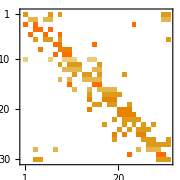

```mathematica
Clear[S,n,β]
n=30;
β=0.45; (* 0.35 *)
(*S=MakeCloseConnectedDiffusionNoDiag[β,n]//N;*)
S=MakeCloseConnectedDiffusion[β,n]//N;
MatrixPlot[S,ImageSize->Small]
```

```mathematica
(*
Clear[S,n,β]
n=30;
β=0.5;
S=MakeExponentialDiffusion[β,n];
MatrixPlot[S,ImageSize->Small]
*)
```

```mathematica
folder="saved1";
S=Import[folder<>"/initialOR.csv"];
n=Length[S];
```

```mathematica
Show[CreateWeightedGraphImage[S,True]]
Show[CreateWeightedGraphImage[MatrixPower[S,6],True]]
```

-Graphics-

-Graphics-

### Run the gradient ascend.

#### Parameter setting Normally: ϵ=0.025

```mathematica
(* DirectionOption:
0: Ascend,
 1: Descend,
 2: Bidirectional
*)
DirectionOption=1;
(* 
0: SR,
1: ST
*)
timeforward=0;
timebackward=10;
ϵ=0.025; (* 0.025 *)
s=3;
(* Calculate required steps *)
stepsf=timeforward/ϵ;
stepsb=timebackward/ϵ;
noise=0;
```

```mathematica
normalize=#/Total[#]&;
prior=UniformP[n];
```

#### Gradient ascend

```mathematica
{time1,outSR}=Timing[Switch[
DirectionOption,
0,SRPerturbationGradientAscend[S,s,ϵ,stepsf,prior,noise],
1,SRPerturbationGradientAscend[S,s,-ϵ,stepsb,prior,noise],
2,PerturbationGradientBidirectional[S,s,ϵ,stepsf,stepsb,0,prior,noise]
]];
{time2,outST}=Timing[Switch[
DirectionOption,
0,STPerturbationGradientAscend[S,s,ϵ,stepsf,prior,noise],
1,STPerturbationGradientAscend[S,s,-ϵ,stepsb,prior,noise],
2,PerturbationGradientBidirectional[S,s,ϵ,stepsf,stepsb,1,prior,noise]
]];
ticks=Switch[
DirectionOption,
0,Table[i*ϵ,{i,0,stepsf}],
1,Table[i*ϵ,{i,0,stepsb}],
2,Table[i*ϵ,{i,-stepsb,stepsf}]
];
srOR=outSR⟦1⟧;
stOR=outSR⟦2⟧;
graphSR=outSR⟦3⟧;
srPathOR=Flatten[Transpose[outSR⟦3⟧,{3,2,1}],1];
minimalOR=First[outSR⟦3⟧];
initialOR=Switch[DirectionOption,
0,outSR⟦3,1⟧,
1,outSR⟦3,1⟧,
2,outSR⟦3,stepsb+1⟧
];
maximalOR=Last[outSR⟦3⟧];
srOT=outST⟦1⟧;
stOT=outST⟦2⟧;
graphST=outST⟦3⟧;
srPathOT=Flatten[Transpose[outST⟦3⟧,{3,2,1}],1];
minimalOT=First[outST⟦3⟧];
initialOT=Switch[DirectionOption,
0,outST⟦3,1⟧,
1,outST⟦3,1⟧,
2,outST⟦3,stepsb+1⟧
];
maximalOT=Last[outST⟦3⟧];
Print["Total time: ",time1+time2]
```

Total time: 2454.99

```mathematica
(*
folder="saved1";
Export[folder<>"/srOR.csv",srOR];
Export[folder<>"/srOT.csv",srOT];
Export[folder<>"/stOR.csv",stOR];
Export[folder<>"/stOT.csv",stOT];
Export[folder<>"/minimalOR.csv",minimalOR];
Export[folder<>"/minimalOT.csv",minimalOT];
Export[folder<>"/maximalOR.csv",maximalOR];
Export[folder<>"/maximalOT.csv",maximalOT];
Export[folder<>"/initialOR.csv",initialOR];
Export[folder<>"/initialOT.csv",initialOT];
Export[folder<>"/graphSR.mx",graphSR,"MX"];
Export[folder<>"/graphST.mx",graphST,"MX"];
*)
```

### Create images.

```mathematica
(*
folder="saved1";
srOR=Import[folder<>"/srOR.csv"];
srOT=Import[folder<>"/srOT.csv"];
stOR=Import[folder<>"/stOR.csv"];
stOT=Import[folder<>"/stOT.csv"];
minimalOR=Import[folder<>"/minimalOR.csv"];
minimalOT=Import[folder<>"/minimalOT.csv"];
maximalOR=Import[folder<>"/maximalOR.csv"];
maximalOT=Import[folder<>"/maximalOT.csv"];
initialOR=Import[folder<>"/initialOR.csv"];
initialOT=Import[folder<>"/initialOT.csv"];
n=Length[initialOR];
prior=UniformP[n];
graphSR=Import[folder<>"/graphSR.mx"];
graphST=Import[folder<>"/graphST.mx"];
*)
```

```mathematica
width=1.5*512;
height=0.5*width;
gwidth=0.23width; (* 0.3 width *)
gheight=0.23width;
ratio=0.45;
graphSize=width×{0.23,0.23};
cutoff=0.025;
arrowsize=0.025;
showweights=True;
thickness=0.5;
vertexsize=0.3;
minimalGraphOR=CreateWeightedGraphImage[minimalOR,showweights,cutoff,arrowsize,thickness,vertexsize];
initialGraphOR=CreateWeightedGraphImage[initialOR,showweights,cutoff,arrowsize,thickness,vertexsize];
maximalGraphOR=CreateWeightedGraphImage[maximalOR,showweights,cutoff,arrowsize,thickness,vertexsize];
minimalGraphOT=CreateWeightedGraphImage[minimalOT,showweights,cutoff,arrowsize,thickness,vertexsize];
initialGraphOT=CreateWeightedGraphImage[initialOT,showweights,cutoff,arrowsize,thickness,vertexsize];
maximalGraphOT=CreateWeightedGraphImage[maximalOT,showweights,cutoff,arrowsize,thickness,vertexsize];
graphsOT=Grid[{{
Framed[Panel[Show[minimalGraphOT,ImageSize->{gwidth,gheight}],Background->White]],
Framed[Panel[Show[initialGraphOT,ImageSize->{gwidth,gheight}],Background->White]],
Framed[Panel[Show[maximalGraphOT,ImageSize->{gwidth,gheight}],Background->White]]
}}];
graphsOR=Grid[{{
Framed[Panel[Show[minimalGraphOR,ImageSize->{gwidth,gheight}],Background->White]],
Framed[Panel[Show[initialGraphOR,ImageSize->{gwidth,gheight}],Background->White]],
Framed[Panel[Show[maximalGraphOR,ImageSize->{gwidth,gheight}],Background->White]]
}}];
```

```mathematica
minValOR=First@First@srOR;
maxValOR=First@Last@srOR;
minValOT=First@First@srOT;
maxValOT=First@Last@srOT;
maxOR=Max[{Max[Last/@srOR],Max[Last/@stOR]}];
minOR=Min[{Min[Last/@srOR],Min[Last/@stOR]}];
maxOT=Max[{Max[Last/@srOT],Max[Last/@stOT]}];
minOT=Min[{Min[Last/@srOT],Min[Last/@stOT]}];
posMinGOR={-0.75*timebackward,minOR+0.55(maxOR-minOR)};
posOrGOR={0.2*timeforward,minOR+0.1(maxOR-minOR)};
posMaxGOR={0.75*timeforward,minOR+0.1(maxOR-minOR)};
posMinGOT={-0.75*timebackward,minOT+0.5(maxOT-minOT)};
posOrGOT={0.15*timeforward,minOT+0.5(maxOT-minOT)};
posMaxGOT={0.75*timeforward,minOT+0.5(maxOT-minOT)};
```

```mathematica
lineAOR={Thick,Red,Dashed,Line[{{minValOR,0},{minValOR,5}}]};
lineAOT={Thick,Red,Dashed,Line[{{minValOT,0},{minValOT,5}}]};
lineB={Thick,Red,Dashed,Line[{{0,0},{0,5}}]};
lineCOR={Thick,Red,Dashed,Line[{{maxValOR,0},{maxValOR,5}}]};
lineCOT={Thick,Red,Dashed,Line[{{maxValOT,0},{maxValOT,5}}]};
maxSRLineOR={Thick,Gray,Dotted,Line[{{minValOR,H[prior]},{maxValOR,H[prior]}}]};
maxSRLineOT={Thick,Gray,Dotted,Line[{{minValOT,H[prior]},{maxValOT,H[prior]}}]};
maxSTLineOR={Thick,Purple,Dashed,Line[{{minValOR,Log[n]//N},{maxValOR,Log[n]//N}}]};
maxSTLineOT={Thick,Purple,Dashed,Line[{{minValOT,Log[n]//N},{maxValOT,Log[n]//N}}]};
```

## Main figure

```mathematica
min=-4;
max=1.5;
filterSrOT=Select[srOT,min≤#⟦1⟧≤max&];
filterStOT=Select[stOT,min≤#⟦1⟧≤max&];
filterSrOR=Select[srOR,min≤#⟦1⟧≤max&];
filterStOR=Select[stOR,min≤#⟦1⟧≤max&];
```

```mathematica
stepOT1=-33; (* 20.3% *)
stepOT2=-20; (* 10% *)
stepOT3=0;
stepOT4=11; (* -10.1% *)
stepOR1=-65; (* 20% *)
stepOR2=-41; (* 10% *)
stepOR3=0;
stepOR4=11;(* -9% *)
```

```mathematica
markOT1=First@srOT⟦stepsb+1+stepOT1⟧;
markOT2=First@srOT⟦stepsb+1+stepOT2⟧;
markOT3=First@srOT⟦stepsb+1+stepOT3⟧;
markOT4=First@srOT⟦stepsb+1+stepOT4⟧;
markOR1=First@srOT⟦stepsb+1+stepOR1⟧;
markOR2=First@srOT⟦stepsb+1+stepOR2⟧;
markOR3=First@srOT⟦stepsb+1+stepOR3⟧;
markOR4=First@srOT⟦stepsb+1+stepOR4⟧;
```

```mathematica
aratio=0.5;
lineOT1={Thick,Blue,Dashed,Line[{{markOT1,0},{markOT1,10}}]};
lineOT2={Thick,Magenta,Dashed,Line[{{markOT2,0},{markOT2,10}}]};
lineOT3={Thick,Red,Dashed,Line[{{markOT3,0},{markOT3,10}}]};
lineOT4={Thick,Gray,Dashed,Line[{{markOT4,0},{markOT4,10}}]};
lineOR1={Thick,Blue,Dashed,Line[{{markOR1,0},{markOR1,10}}]};
lineOR2={Thick,Magenta,Dashed,Line[{{markOR2,0},{markOR2,10}}]};
lineOR3={Thick,Red,Dashed,Line[{{markOR3,0},{markOR3,10}}]};
lineOR4={Thick,Gray,Dashed,Line[{{markOR4,0},{markOR4,10}}]};
```

```mathematica
scaleparam=0.5;
gwidth2=130;
gheight2=Ceiling[0.93*125];
gsizeA={130,120};
gsizeB={130,117};
letterColor=Red;
gfont=scaleparam*40;
graphA=Framed[Panel[Show[CreateWeightedGraphImage[graphSR⟦stepsb+1+stepOR1⟧,True],ImageSize->gsizeA],Style["a",gfont,FontFamily->"Times",Black,Bold],Background->White]];
graphB=Framed[Panel[Show[CreateWeightedGraphImage[graphSR⟦stepsb+1+stepOR2⟧,True],ImageSize->gsizeB],Style["b",gfont,FontFamily->"Times",Black,Bold],Background->White]];
graphC=Framed[Panel[Show[CreateWeightedGraphImage[graphSR⟦stepsb+1+stepOR3⟧,True],ImageSize->gsizeA],Style["c",gfont,FontFamily->"Times",Black,Bold],Background->White]];
graphD=Framed[Panel[Show[CreateWeightedGraphImage[graphSR⟦stepsb+1+stepOR4⟧,True],ImageSize->gsizeB],Style["d",gfont,FontFamily->"Times",Black,Bold],Background->White]];
graphE=Framed[Panel[Show[CreateWeightedGraphImage[graphST⟦stepsb+1+stepOT1⟧,True],ImageSize->gsizeA],Style["e",gfont,FontFamily->"Times",Black,Bold],Background->White]];
graphF=Framed[Panel[Show[CreateWeightedGraphImage[graphST⟦stepsb+1+stepOT2⟧,True],ImageSize->gsizeB],Style["f",gfont,FontFamily->"Times",Black,Bold],Background->White]];
graphG=Framed[Panel[Show[CreateWeightedGraphImage[graphST⟦stepsb+1+stepOT3⟧,True],ImageSize->gsizeA],Style["g",gfont,FontFamily->"Times",Black,Bold],Background->White]];
graphH=Framed[Panel[Show[CreateWeightedGraphImage[graphST⟦stepsb+1+stepOT4⟧,True],ImageSize->gsizeB],Style["h",gfont,FontFamily->"Times",Black,Bold],Background->White]];
```

```mathematica
sdims=scaleparam*1.04{1306,653};
srImageOT=ListLinePlot[{filterSrOT,filterStOT},ImageSize->sdims,AspectRatio->ratio,PlotStyle->{Black,Blue},Frame->True,FrameStyle->Thick,FrameTicksStyle->Directive[fontsize,Black],
Axes->None,AxesStyle->Dashed,PlotRange->{1,3.5},
FrameLabel->{Style["Perturbation parameter, λ",fontsize,FontFamily->"Times",Black],Style["Entropy",fontsize,FontFamily->"Times",Black]},
Epilog->{lineOT1,lineOT2,lineOT3,lineOT4,maxSTLineOT,
Inset[Framed[Text[Style["Extremizing predictability",fontsize,Black,FontFamily->"Times"]],Background->White],Scaled[{0.5,.93}]],
Style[Text["(a)",{-1.95,3}],fontsize,Blue,FontFamily->"Times"],
Style[Text["(b)",{-1.225,3}],fontsize,Magenta,FontFamily->"Times"],
Style[Text["(c)",{-0.2,3}],fontsize,Red,FontFamily->"Times"],
Style[Text["(d)",{0.9,3}],fontsize,Gray,FontFamily->"Times"],
Style[Text["i",{-3.9,3.25}],fontsize,Black,FontFamily->"Times"]
}];
srImageOR=ListLinePlot[{filterSrOR,filterStOR},ImageSize->sdims,AspectRatio->ratio,PlotStyle->{Black,Blue},Frame->True,FrameStyle->Thick,FrameTicksStyle->Directive[fontsize,Black],
Axes->None,AxesStyle->Dashed,PlotRange->{1,3.5},
FrameLabel->{Style["Perturbation parameter, λ",fontsize,FontFamily->"Times",Black],Style["Entropy",fontsize,FontFamily->"Times",Black]},
Epilog->{{lineOR1,lineOR2,lineOR3,lineOR4,maxSTLineOR},
Inset[Framed[Text[Style["Extremizing retrodictability",fontsize,Black,FontFamily->"Times"]],Background->White],Scaled[{0.5,.93}]],
Style[Text["(e)",{-3.35,3}],fontsize,Blue,FontFamily->"Times"],
Style[Text["(f)",{-2,3}],fontsize,Magenta,FontFamily->"Times"],
Style[Text["(g)",{-0.2,3}],fontsize,Red,FontFamily->"Times"],
Style[Text["(h)",{0.94,3}],fontsize,Gray,FontFamily->"Times"],
Style[Text["j",{-3.9,3.25}],fontsize,Black,FontFamily->"Times"],Inset[LineLegend[{Black,Blue},{"⟨S_R⟩, Ret. entropy","⟨S_T⟩, Pred. entropy"},LegendLayout->"Column",LabelStyle->fontsize,LegendFunction->(Framed[#,Background->White]&)],Scaled[{0.78,0.22}]]}];
```

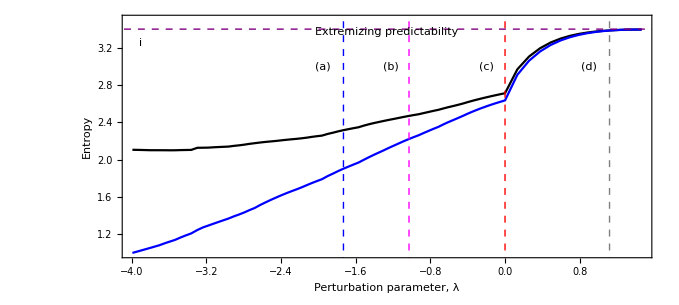
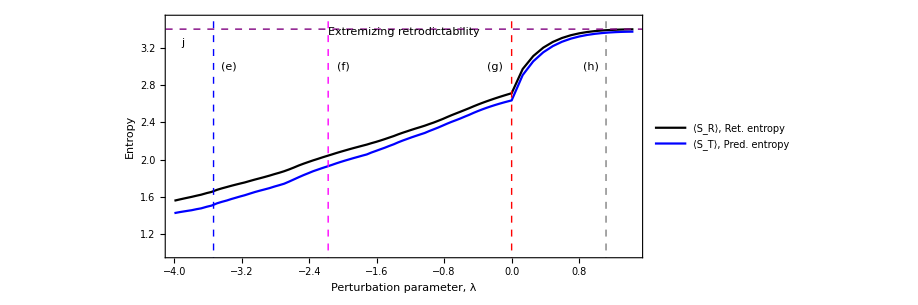
-Graphics-a | -Graphics-b | -Graphics-c | -Graphics-d | -Graphics-e | -Graphics-f | -Graphics-g | -Graphics-h
-Graphics- | -Graphics-

```mathematica
image=Grid[{{Grid[{{graphA,graphB,graphC,graphD}}],Grid[{{graphE,graphF,graphG,graphH}}]},{srImageOT,srImageOR}}]
```

```mathematica
(*Export["extremizing-figure.eps",image];*)
```

## Improvement

### Generate Data

```mathematica
First@Timing[
dataSR=TheoreticalAccuracy[#,s,prior]&/@graphSR;
dataST=TheoreticalAccuracy[#,s,prior]&/@graphST;
];
{srORdat,stORdat}=100Transpose[dataSR];
{srOTdat,stOTdat}=100Transpose[dataST];
ticksOR=First/@srOR;
ticksOT=First/@srOT;
λsrORdat=Transpose[{ticksOR,srORdat}];
λstORdat=Transpose[{ticksOR,stORdat}];
λsrOTdat=Transpose[{ticksOT,srOTdat}];
λstOTdat=Transpose[{ticksOT,stOTdat}];
```

```mathematica
(*
Export[folder<>"/lsrORdatS.csv",λsrORdatS];
Export[folder<>"/lstORdatS.csv",λstORdatS];
Export[folder<>"/lsrOTdatS.csv",λsrOTdatS];
Export[folder<>"/lstOTdatS.csv",λstOTdatS];
*)
```

```mathematica
(*
λsrORdatS=Import[folder<>"/lsrORdatS.csv"];
λstORdatS=Import[folder<>"/lstORdatS.csv"];
λsrOTdatS=Import[folder<>"/lsrOTdatS.csv"];
λstOTdatS=Import[folder<>"/lstOTdatS.csv"];
*)
```

```mathematica
minVal=Max[minValOR,minValOT];
maxVal=1;(*Min[maxValOR,maxValOT];*)
λsrORdatS=Select[λsrORdat,minVal<=#⟦1⟧≤maxVal&];
λstORdatS=Select[λstORdat,minVal<=#⟦1⟧≤maxVal&];
λsrOTdatS=Select[λsrOTdat,minVal<=#⟦1⟧≤maxVal&];
λstOTdatS=Select[λstOTdat,minVal<=#⟦1⟧≤maxVal&];
baseline={{minVal,100/n},{maxVal,100/n}};
vertLine={Thick,Dashed,Black,Line[{{0,0},{0,100}}]};
```

```mathematica
filterλsrORdat=Select[λsrORdat,min≤#⟦1⟧≤max&];
filterλstORdat=Select[λstORdat,min≤#⟦1⟧≤max&];
filterλsrOTdat=Select[λsrOTdat,min≤#⟦1⟧≤max&];
filterλstOTdat=Select[λstOTdat,min≤#⟦1⟧≤max&];
```

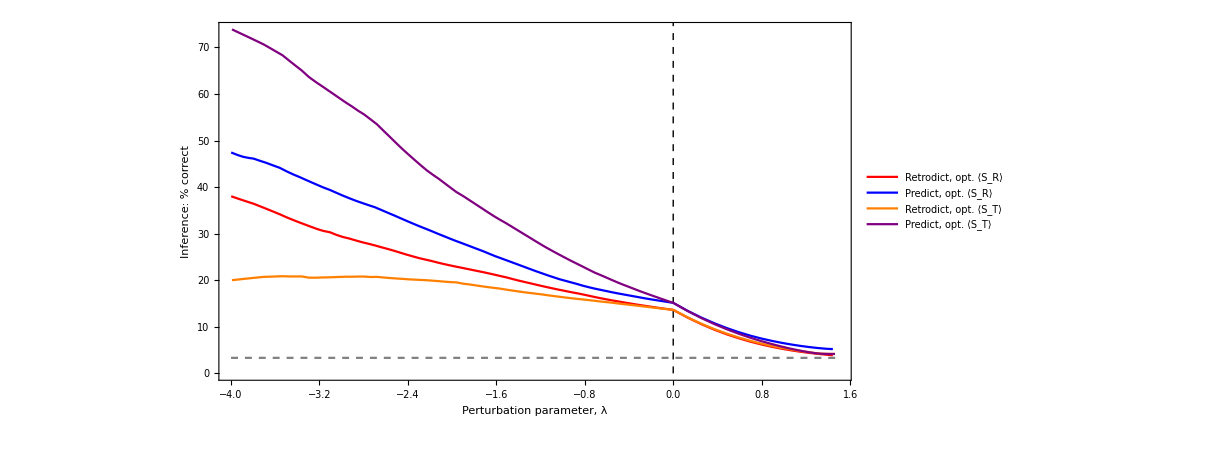

```mathematica
font1=30;
baseline={{min,10./3.},{max,10./3.}};
zoomed=ListLinePlot[{filterλsrORdat,filterλstORdat,filterλsrOTdat,filterλstOTdat,baseline},PlotRange->All,AspectRatio->0.5,Frame->True,ImageSize->{900,450},AxesStyle->Dashed,Axes->None,PlotStyle->{Red,Blue,Orange,Purple,{Gray,Dashed}},FrameStyle->Thick,FrameTicksStyle->Directive[font1,Black,FontFamily->"Times"],
AxesStyle->Dashed,
FrameLabel->{Style["Perturbation parameter, λ",font1,FontFamily->"Times",Black],Style["Inference: % correct",font1,FontFamily->"Times",Black]},
Prolog->{vertLine,Inset[LineLegend[{Red,Blue,Orange,Purple},{"Retrodict, opt. ⟨S_R⟩","Predict, opt. ⟨S_R⟩","Retrodict, opt. ⟨S_T⟩","Predict, opt. ⟨S_T⟩"},LegendLayout->"Column",LabelStyle->Directive[28,Black,FontFamily->"Times"],LegendFunction->(Framed[#,Background->White]&)],Scaled[{0.79,0.7}]]}]
```

```mathematica
(*Export["Improvement.eps",zoomed];*)
```

## Extremal graph figures

```mathematica
graphSRs6=Import[folder<>"/graphSR-s6.mx"];
graphSTs6=Import[folder<>"/graphST-s6.mx"];
extremeSRs6=Import[folder<>"/extreme-SR-s6.csv"];
extremeSTs6=Import[folder<>"/extreme-ST-s6.csv"];
```

```mathematica
gsize1={300,309};
gsize2={300,300};
gfont=28;
Last@λstOTdat⟦1⟧;
Last@({1,100}*TheoreticalAccuracy[graphSTs6,s,prior]);
Last@λsrORdat⟦98⟧;
Last@({1,100}*TheoreticalAccuracy[graphSRs6,s,prior]);
highLambda=Grid[{{
Framed[Panel[Show[CreateWeightedGraphImage[graphST⟦1⟧,True],ImageSize->gsize1],Style["a",gfont,FontFamily->"Times",Black],Background->White]],
Framed[Panel[Show[CreateWeightedGraphImage[graphSTs6,True],ImageSize->gsize2],Style["b",gfont,FontFamily->"Times",Black],Background->White]]},
{Framed[Panel[Show[CreateWeightedGraphImage[graphSR⟦98⟧,True],ImageSize->gsize1],Style["c",gfont,FontFamily->"Times",Black],Background->White]],
Framed[Panel[Show[CreateWeightedGraphImage[graphSRs6,True],ImageSize->gsize2],Style["d",gfont,FontFamily->"Times",Black],Background->White]]}}]
```

-Graphics-a | -Graphics-b
-Graphics-c | -Graphics-d

```mathematica
Export["highLambda.eps",highLambda];
```

## Performance improvement

#### δs: steps to move (away from λ=0 - origin) True: Optimize <SR> False: Optimize <ST>

```mathematica
(* Change these parts *)
δs=-33;
type=False;
(* Let all this just run *)
If[type,
λdata=λsrORdat;entropy=srOR;graphS=graphSR,
λdata=λstOTdat;entropy=stOT;graphS=graphST;
];
initial=initialOR; (* same as initialOT *)
origin=stepsb+1;
step=origin+δs; (* Pick which step to look at *)
Print["Difference in success: ", λdata⟦step,2⟧-λdata⟦origin,2⟧, "%"]
Print["Original: ",λdata⟦origin,2⟧]
Print["Success rate: ",λdata⟦step,2⟧,"\nDistance: λ=",λdata⟦step,1⟧ ]
Print["Entropy: ",entropy⟦step,2⟧]
graph=graphS⟦step⟧;
Print["L^2 distance: ",√(Total@(#^2&/@Flatten[graph-initial]))]
Print["L^1 distance: ",Total@(Abs/@Flatten[graph-initial])]
Print["Max element change: ",Max@(Abs/@Flatten[graph-initial])]
Print["Elements changed by ≥ 0.1: ",Select[Abs/@Flatten[graph-initial],#≥0.1&]//Length]
Print["Original nonzero element: ",Total[If[#>0,1,0]&/@Flatten[initial]]]
Grid[{{
CreateWeightedGraphImage[graph,True,0.025,0.025,0.5,0.3],
CreateWeightedGraphImage[initial,True,0.025,0.025,0.5,0.3]
}}]
```

Difference in success: 20.3025%

Original: 15.1469

Success rate: 35.4494
Distance: λ=-1.73079

Entropy: 1.90467

L^2 distance: 1.40994

L^1 distance: 12.6301

Max element change: 0.358713

Elements changed by ≥ 0.1: 56

Original nonzero element: 126

-Graphics- | -Graphics-